# Mathematica for Research Assignment- VII

## Masters in Data and Computational Science Ashwath Paul John Vinodh [ 18203754]

## Date Submitted: 07/11/2018 Due Date: 08/11/2018

# Assignment 7

### Analytically solving equations

Find the cube roots of 1 (three of them) by writing out a suitable equation to solve and then using Solve. Print out approximate numerical values. Check that you’ve found the right values by substituting back into the equation you solved.

```mathematica
Clear[x]
```

```mathematica
eq=x^3-1==0//Solve
```

{{x→1},{x→-(-1)^(1/3)},{x→(-1)^(2/3)}}

```mathematica
N[eq]
```

{{x→1.},{x→-0.5-0.866025 ⅈ},{x→-0.5+0.866025 ⅈ}}

```mathematica
y=Reduce[x^3-1==0,x]
```

x==1||x==-(-1)^(1/3)||x==(-1)^(2/3)

```mathematica
values=ComplexExpand[y]
```

x==1||x==-1/2-(ⅈ √3)/2||x==-1/2+(ⅈ √3)/2

```mathematica
Equate=If[x^3-1==0,TRUE,FALSE]
```

If[-1+x^3==0,TRUE,FALSE]

```mathematica
Equate/.x-> 1
```

TRUE

```mathematica
Equate/.x->-(-1)^(1/3)
```

TRUE

```mathematica
Equate/.x->(-1)^(2/3)
```

TRUE

```mathematica
Equate/.x->  1
```

TRUE

```mathematica
Equate/.x->( -1/2-(ⅈ √3)/2)
```

TRUE

```mathematica
Equate/.x->( -1/2+(ⅈ √3)/2)
```

TRUE

Find the range of values for x for which x^2+3x>0. Hint: look up the Reduce function.

```mathematica
Reduce[x^2+3x>0,x]
```

x<-3||x>0

Compare the solution of Cos[x]=0 using Solve and Reduce.

```mathematica
Clear[x]
```

```mathematica
Solve[Cos[x]==0,x]
```

{{x→ConditionalExpression[-π/2+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[π/2+2 π C[1],C[1]∈ℤ]}}

```mathematica
Reduce[Cos[x]==0,x]
```

C[1]∈ℤ&&(x==-π/2+2 π C[1]||x==π/2+2 π C[1])

```mathematica
The  difference between Reduce and Solve is that Reduce gives all the possible solutions to a set of equations,while Solve gives only the generic ones.
```

Consider the 5th order polynomial a x^5+b x^4+c x^3+d x^2+e x+f. Make a Manipulate that finds all 5 roots (solves for x) in the complex plane for this polynomial (choose slider controls for each coefficient a, b, c, d, e and f with small ranges [-2,2] for each). The result should be a list of 5 complex numbers corresponding to the 5 roots. By using the real part of the solutions for x coordinates and the imaginary part for y coordinates, use ListPlot to plots the roots. Fix the plot range to {{-2,2},{-2,2}} so that its possible to see how the roots move.

```mathematica
Clear[x,a,b,c,d,e,f]
```

```mathematica
Manipulate[ListPlot[ReIm[x/.Solve[a x^5+b x^4+c x^3+d x^2+e x+f==0,x]],PlotRange->{{-2,2},{-2,2}},PlotTheme->"Marketing"],{a,-2,2},{b,-2,2},{c,-2,2},{d,-2,2},{e,-2,2},{f,-2,2}]
```

Create a polynomial with 5 real roots (Hint: a polynomial crosses the axis and has a root at x=x_0 iff it has a factor (x-x_0).) and use Solve to find the roots. Verify that your polynomial has 5 roots by plotting it and checking it crosses the axis 5 times.

```mathematica
(* rt1=Decompose[(x+1)(x-2)(x+3)(x-4)(x+5),x] *)
```

```mathematica
eq1=120+94 x-51 x^2-23 x^3+3 x^4+x^5==0
```

120+94 x-51 x^2-23 x^3+3 x^4+x^5==0

```mathematica
Solve[eq1,x]
```

{{x→-5},{x→-3},{x→-1},{x→2},{x→4}}

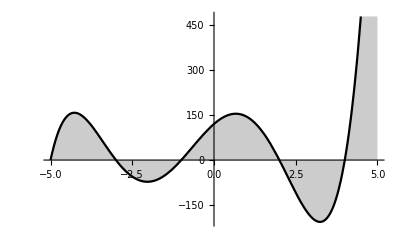

```mathematica
Plot[rt1,{x,-5,5},Filling-> Axis,PlotTheme->"Monochrome"]
```

### Numerically solving

Use NSolve to find all 5 roots of the polynomial from the previous question.

```mathematica
abcde=NSolve[abcd]
```

{{x→-1.07043},{x→-0.690101-1.45374 ⅈ},{x→-0.690101+1.45374 ⅈ},{x→0.475316-1.01819 ⅈ},{x→0.475316+1.01819 ⅈ}}

The product log function is defined to be to solution for x≥-1/ⅇ of the equation y=x ⅇ^x. Define a function that, given a y value, uses FindRoot to determine an x value.

```mathematica
Clear[x]
```

```mathematica
prod[y_]:=FindRoot[y==x*ⅇ^x,{x,-1/ⅇ}]/;x≥ -1/ⅇ
```

```mathematica
prod[2]
```

{x→0.852606}

```mathematica
ProductLog[2.0]
```

0.852606

Plot your function from the previous question and compare against a plot of the built-in ProductLog function. In this case you could have just used ProductLog, but in general there may not be an exact solution and the FindRoot method can be useful.

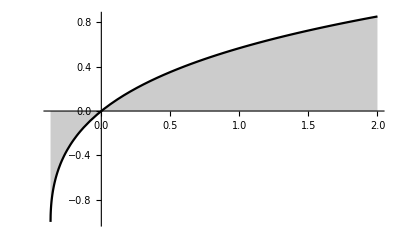

```mathematica
Plot[x/.prod[y],{y,-1/ⅇ,2},Filling-> Axis,PlotTheme->"Monochrome"]
```

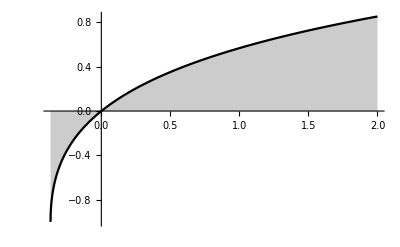

```mathematica
Plot[ProductLog[y],{y,-1/ⅇ,2},Filling-> Axis,PlotTheme->"Monochrome"]
```

In the previous question you could have just used ProductLog, but in general there may not be an exact solution and the FindRoot method can be useful. Consider the implicit equation u-π==w^-1(1-Cos[w])-1/2 w. In this case Reduce and Solve can’t find a solution for w as a function of u. Write a function which uses FindRoot to numerically solve for w for a given numeric value of u. (Hint: use w=1 as a starting guess in FindRoot)

```mathematica
imfn[u_]:=FindRoot[u-π==w^-1(1-Cos[w])-1/2 w,{w,1}]
```

```mathematica
imfn[1]
```

{w→4.70923}

Plot the function from the previous question for -2π≤u≤4π

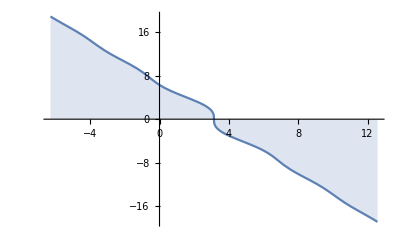

```mathematica
Plot[w/.imfn[u],{u,-2 π,4 π},Filling-> Axis]
```